```mathematica
a0GaN:= Quantity[2×10^5,"Centimeter^(-1)"]
a0AlN:= Quantity[1×10^5,"Centimeter^(-1)"]
E0:=Quantity[6.424,"eV"]
AlN:=Quantity[6.28, "eV"]
GaN:=Quantity[3.44, "eV"]
AlContent:= 0.72
a0:= a0AlN *AlContent+ a0GaN*(1-AlContent)
EG:=AlN×(AlContent)+GaN(1-AlContent)

a:= a0 × √((E0-EG)/EG)
ParallelEvaluate[Off[Part::span]];
ParallelEvaluate[Off[FindFit::fitd]];
ParallelEvaluate[Off[ReplaceAll::reps]];
ParallelEvaluate[Off[Part::pkspec1]];
```

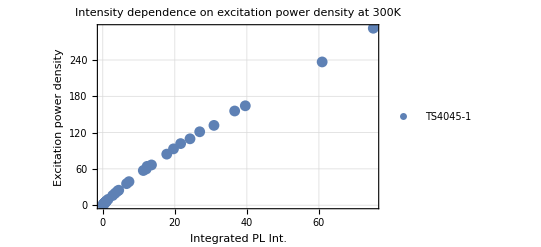
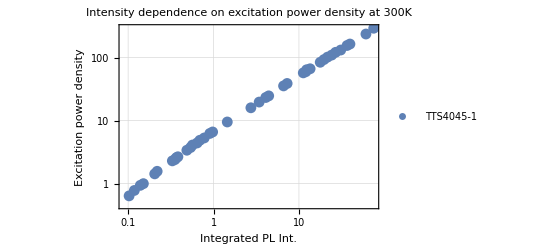

```mathematica
s=N[Import["TS4045-1.txt","Table"]];

Row[{ListPlot[s,PlotRange-> Full, PlotLegends->{TS4045-1},ImageSize->400,PlotLabel-> "Intensity dependence on excitation power density at 300K",
FrameLabel->{Style["Integrated  PL Int.",20],Style["Excitation power density",20]},
PlotTheme->"Detailed"],
ListLogLogPlot[s,PlotRange-> Full, PlotLegends->{TTS4045-1 }, ImageSize->400,PlotLabel-> "Intensity dependence on excitation power density at 300K",
FrameLabel->{Style["Integrated  PL Int.",20],Style["Excitation power density",20]},
PlotTheme->"Detailed"]}]

Clear[x,r]
s1 =ArrayReshape[s,{39,2}] //N;

l1=s1[[All,2]]*x*(1-r)/(QuantityMagnitude[E0])*6.241509*10^21;

o1=s1[[All,1]];

m1= Sort[Transpose[{o1,l1}]];

Manipulate[Row[{ListPlot[N[m1[[ii ;; i]]]  /.x-> α  /.r->R,PlotRange-> Full, PlotLegends->{TS4045-1},
FrameLabel->{Style["Integrated  PL Int.",20],Style["Generationsrate",20]},ImageSize-> 400,
PlotTheme->"Detailed"],ListLogLogPlot[N[m1[[ii ;; i]]]  /.x-> α  /.r->R,PlotRange-> Full, PlotLegends->{TS4045-1},ImageSize->400,
FrameLabel->{Style["Integrated  PL Int.",20],Style["Generationsrate",20]},
PlotTheme->"Detailed"]}],{α, 1*10^4, 1*10^8},{R, 0.1,1.0},{{i,39,"Anzahl Messdaten bis"},1,39,1},{{ii ,20,"Anzahl Messdaten von"},1,39,1}]
```

```mathematica
(*
x:=1*10^5
r:=0.20

Manipulate[
par1=FindFit[m1[[II ;; IJ]],z1*√y+ z2 * 10^y,{z1,z2},y];
a1=(z1/.par1[[1]]);
a2=(z2/.par1[[2]]);
Column[{a1,
a2,
Show[ListPlot[m1[[II ;; IJ]],PlotLegends->{TS4239 , TS2669, TS2672,TS2684},PlotTheme-> "Detailed",ImageSize->400],Plot[  a1*√p+a2*p ,{p,0,6000},PlotRange->Automatic]] ,Show[ListLogLogPlot[m1[[II ;; IJ]],PlotLegends->{TS4239 , TS2669, TS2672,TS2684},PlotTheme-> "Detailed",ImageSize->400],LogLogPlot[  a1*√p+a2*p ,{p,1*10^-5,6000},PlotRange->Automatic]]
}]
,{{II,20,"Anzahl Messdaten bis"},1,61,1},{{IJ,50,"Anzahl Messdaten von"},1,61,1}
]*)
```

```mathematica
par1=FindFit[m1[[1 ;; 20]],b1*√y+b2 * y,{b1,b2},y]
a1=(b1/.par1[[1]])
a2=(b2/.par1[[2]])
```

{b1→1.20322×10^21 (1-r) x,b2→5.09941×10^21 (1-r) x}

1.20322×10^21 (1-r) x

5.09941×10^21 (1-r) x

```mathematica
Clear["Global`*"]
```

```mathematica
Plot[  a1*√p+a2*p ,{p,0,6000},PlotRange->Automatic]
```

-Graphics-

```mathematica
par5[n_,m_]:=FindFit[m1[[n ;; m]],z1*√y+ z2 * y,{z1,z2},y];
a111:=(z1/.par5[[1]]);
a222:=(z2/.par5[[2]]);
x:=1*10^5
r:=0.20


Manipulate[eins:=par5[n,m];
a111:=(z1/.eins[[1]]);
a222:=(z2/.eins[[2]]);

Column[

Show[ListPlot[m1[[n ;; m]],PlotLegends->{TS4045-1},PlotTheme-> "Detailed",ImageSize->400],Plot[  a111*√p+a222*p ,{p,0,6000},PlotRange->Automatic]] ,Show[ListLogLogPlot[m1[[n ;;m]],PlotLegends->{TTS4045-1},PlotTheme-> "Detailed",ImageSize->400],LogLogPlot[  a111*√p+a222*p ,{p,1*10^-5,6000},PlotRange->Automatic]]
]
,{{n,1,"Anzahl Messdaten bis"},1,39,1},{{m,39,"Anzahl Messdaten von"},1,39,1}
]
```

```mathematica
x:=1*10^5
r:=0.20

ai=1; {Slider[Dynamic[ai],{1,40,1}],Dynamic[ai]}
bi=49;{Slider[Dynamic[bi],{1,49,1}],Dynamic[bi]}
```

{,}

{,}

```mathematica
par5[ai_,bi_]:=FindFit[m1[[ai ;; bi]],z1*√y+ z2 * y,{z1,z2},y]
eins := par5[ai,bi]
a111:=(z1/.eins[[1]])
a222:=(z2/.eins[[2]])
Erg1:=Solve[a111/√a222*B1 + B1^2 == m1[[n,2]],B1]
Ergebnisse =Table[Erg1,{n,ai,bi,1}];

anm=B1/.Ergebnisse[[;;,2]];
IQE1Tab = anm[[;;]]^2/m1[[ai;; bi,2]];
snew:=Sort[s[[;;,2]]]
snew1:= snew[[ai;;bi]]
t11:=Transpose[{snew1,IQE1Tab}]
ListLogLogPlot[t11,PlotLegends->Placed[{TS3931 },{0.85,0.25}],PlotStyle->{Black, Red,Blue, Magenta},PlotRange->Full, PlotTheme->"Detailed",AspectRatio-> 0.8/1,AxesLabel->{"IQE","Excitation Power Density"}]
```

Part::take: Cannot take positions 1 through 49 in m1.

FindFit::fitd: First argument m1 ⟦ 1 ;; 49 ⟧ in FindFit is not a list or a rectangular array.

ReplaceAll::reps: {m1 ⟦ 1 ;; 49 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::take: Cannot take positions 1 through 49 in m1.

FindFit::fitd: First argument m1 ⟦ 1 ;; 49 ⟧ in FindFit is not a list or a rectangular array.

ReplaceAll::reps: {√y\ z1 + y\ z2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification m1 ⟦ 1, 2 ⟧ is longer than depth of object.

Part::take: Cannot take positions 1 through 49 in m1.

General::stop: Further output of Part :: take will be suppressed during this calculation.

FindFit::fitd: First argument m1 ⟦ 1 ;; 49 ⟧ in FindFit is not a list or a rectangular array.

General::stop: Further output of FindFit :: fitd will be suppressed during this calculation.

Part::partd: Part specification m1 ⟦ 2, 2 ⟧ is longer than depth of object.

Part::partd: Part specification m1 ⟦ 3, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 49 in m1.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::take: Cannot take positions 1 through 49 in Symbol[].

Transpose::nmtx: The first two levels of {Symbol[] ⟦ 1 ;; 49 ⟧, {(√Times[« 2 »] + Times[« 2 »] - z1/. Part[« 2 »]/√ReplaceAll[« 2 »])^2/4\ m1 ⟦ 1 ;; 49, 2 ⟧, (√Times[« 2 »] + Times[« 2 »] - z1/. Part[« 2 »]/√ReplaceAll[« 2 »])^2/4\ m1 ⟦ 1 ;; 49, 2 ⟧, « 45 », (√Times[« 2 »] + Times[« 2 »] - z1/. Part[« 2 »]/√ReplaceAll[« 2 »])^2/4\ m1 ⟦ 1 ;; 49, 2 ⟧, (√Times[« 2 »] + Times[« 2 »] - z1/. Part[« 2 »]/√ReplaceAll[« 2 »])^2/4\ m1 ⟦ 1 ;; 49, 2 ⟧}} cannot be transposed.

Transpose::nmtx: The first two levels of {Symbol[] ⟦ 1 ;; 49 ⟧, {0.25\ (√Times[« 2 »] + Times[« 2 »] - 1.\ (z1/. Part[« 2 »])/√ReplaceAll[« 2 »])^2/m1 ⟦ 1 ;; 49, 2 ⟧, « 47 », 0.25\ (√Times[« 2 »] + Times[« 2 »] - 1.\ (z1/. Part[« 2 »])/√ReplaceAll[« 2 »])^2/m1 ⟦ 1 ;; 49, 2 ⟧}} cannot be transposed.

Transpose::nmtx: The first two levels of {Symbol[] ⟦ 1 ;; 49 ⟧, {0.25\ (√Times[« 2 »] + Times[« 2 »] - 1.\ (z1/. Part[« 2 »])/√ReplaceAll[« 2 »])^2/m1 ⟦ 1 ;; 49, 2 ⟧, 0.25\ (√Times[« 2 »] + Times[« 2 »] - 1.\ (z1/. Part[« 2 »])/√ReplaceAll[« 2 »])^2/m1 ⟦ 1 ;; 49, 2 ⟧, « 46 », 0.25\ (√Times[« 2 »] + Times[« 2 »] - 1.\ (z1/. Part[« 2 »])/√ReplaceAll[« 2 »])^2/m1 ⟦ 1 ;; 49, 2 ⟧}} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

ListLogLogPlot::lpn: Transpose[{Symbol[] ⟦ 1 ;; 49 ⟧, {0.25\ (√Plus[« 2 »] - 1.\ ReplaceAll[« 2 »]\ Power[« 2 »])^2/m1 ⟦ 1 ;; 49, 2 ⟧, 0.25\ (√Plus[« 2 »] - 1.\ ReplaceAll[« 2 »]\ Power[« 2 »])^2/m1 ⟦ 1 ;; 49, 2 ⟧, 0.25\ (√Plus[« 2 »] - 1.\ ReplaceAll[« 2 »]\ Power[« 2 »])^2/m1 ⟦ 1 ;; 49, 2 ⟧, « 44 », 0.25\ (√Plus[« 2 »] - 1.\ ReplaceAll[« 2 »]\ Power[« 2 »])^2/m1 ⟦ 1 ;; 49, 2 ⟧, 0.25\ (√Plus[« 2 »] - 1.\ ReplaceAll[« 2 »]\ Power[« 2 »])^2/m1 ⟦ 1 ;; 49, 2 ⟧}}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogLogPlot :: lpn will be suppressed during this calculation.

ListLogLogPlot[Transpose[{Symbol[]⟦1;;49⟧,{((√(4 m1⟦1,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦2,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦3,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦4,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦5,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦6,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦7,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦8,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦9,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦10,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦11,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦12,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦13,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦14,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦15,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦16,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦17,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦18,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦19,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦20,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦21,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦22,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦23,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦24,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦25,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦26,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦27,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦28,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦29,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦30,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦31,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦32,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦33,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦34,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦35,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦36,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦37,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦38,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦39,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦40,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦41,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦42,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦43,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦44,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦45,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦46,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦47,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦48,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧),((√(4 m1⟦49,2⟧+(z1/.m1⟦1;;49⟧)^2/(z2/.√y z1+y z2))-(z1/.m1⟦1;;49⟧)/(√(z2/.√y z1+y z2)))^2)/(4 m1⟦1;;49,2⟧)}}],PlotLegends→Placed[{TS3931},{0.85,0.25}],PlotStyle→{-Graphics-,-Graphics-,-Graphics-,-Graphics-},PlotRange→Full,PlotTheme→Detailed,AspectRatio→0.8,AxesLabel→{IQE,Excitation Power Density}]